```mathematica
(*Matrices for the congruence normal form; dim=size of the matrix (for H half of the size) and a=eigenvalue*)
G[dim_]:=Table[If[i+j==dim+1,(-1)^(i+dim),If[i+j==dim+2,(-1)^(i+dim),0]],{i,1,dim},{j,1,dim}];
jordanBlock[a_,dim_]:=SparseArray[{{i_,i_}:>a,{i_,j_}/;j==i+1:>1},{dim,dim}];
H[a_,dim_]:=ArrayFlatten[{{0,IdentityMatrix[dim]},{jordanBlock[a,dim],0}}];
(*The trace condition*)
ToSolve[A_]:=Tr[Transpose[A].Inverse[A]];
(*Direct sum*)
DiSum[A_,B_]:=ArrayFlatten[{{A,0},{0,B}}];
(*Weighted graphs for G*)
TestNum[a_]:=If[Mod[a,2]==0,1,2];
WeightedG[dim_]:=Table[If[i+j==dim+1,TestNum[i+dim],If[i+j==dim+2,TestNum[i+dim],0]],{i,1,dim},{j,1,dim}];
GraphForG[dim_]:=AdjacencyGraph[WeightedG[dim],VertexLabels->Table[i->Placed[i,Center],{i,1,dim}],VertexSize->0.2,EdgeStyle->Directive[Thickness[0.0025],Blue],VertexLabelStyle->Directive[20,Blue,Bold],VertexStyle->Pink,DirectedEdges->True,ImageSize->Large];
(*Weighted Graph for H*)
GraphForH[a_,dim_]:=AdjacencyGraph[H[a,dim],VertexLabels->Table[i->Placed[i,Center],{i,1,2*dim}],VertexSize->0.2,EdgeStyle->Directive[Thickness[0.005],Blue],VertexLabelStyle->Directive[20,Blue,Bold],VertexStyle->Pink,DirectedEdges->True,ImageSize->Large];
```

{(1),(0 | -1
1 | 1),(0 | 0 | 1
0 | -1 | -1
1 | 1 | 0),(0 | 0 | 0 | -1
0 | 0 | 1 | 1
0 | -1 | -1 | 0
1 | 1 | 0 | 0),(0 | 0 | 0 | 0 | 1
0 | 0 | 0 | -1 | -1
0 | 0 | 1 | 1 | 0
0 | -1 | -1 | 0 | 0
1 | 1 | 0 | 0 | 0),(0 | 0 | 0 | 0 | 0 | -1
0 | 0 | 0 | 0 | 1 | 1
0 | 0 | 0 | -1 | -1 | 0
0 | 0 | 1 | 1 | 0 | 0
0 | -1 | -1 | 0 | 0 | 0
1 | 1 | 0 | 0 | 0 | 0),(0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | -1 | -1
0 | 0 | 0 | 0 | 1 | 1 | 0
0 | 0 | 0 | -1 | -1 | 0 | 0
0 | 0 | 1 | 1 | 0 | 0 | 0
0 | -1 | -1 | 0 | 0 | 0 | 0
1 | 1 | 0 | 0 | 0 | 0 | 0),(0 | 0 | 0 | 0 | 0 | 0 | 0 | -1
0 | 0 | 0 | 0 | 0 | 0 | 1 | 1
0 | 0 | 0 | 0 | 0 | -1 | -1 | 0
0 | 0 | 0 | 0 | 1 | 1 | 0 | 0
0 | 0 | 0 | -1 | -1 | 0 | 0 | 0
0 | 0 | 1 | 1 | 0 | 0 | 0 | 0
0 | -1 | -1 | 0 | 0 | 0 | 0 | 0
1 | 1 | 0 | 0 | 0 | 0 | 0 | 0),(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | -1
0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 0
0 | 0 | 0 | 0 | 0 | -1 | -1 | 0 | 0
0 | 0 | 0 | 0 | 1 | 1 | 0 | 0 | 0
0 | 0 | 0 | -1 | -1 | 0 | 0 | 0 | 0
0 | 0 | 1 | 1 | 0 | 0 | 0 | 0 | 0
0 | -1 | -1 | 0 | 0 | 0 | 0 | 0 | 0
1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0),(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | -1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | -1 | -1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | -1 | -1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | -1 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)}

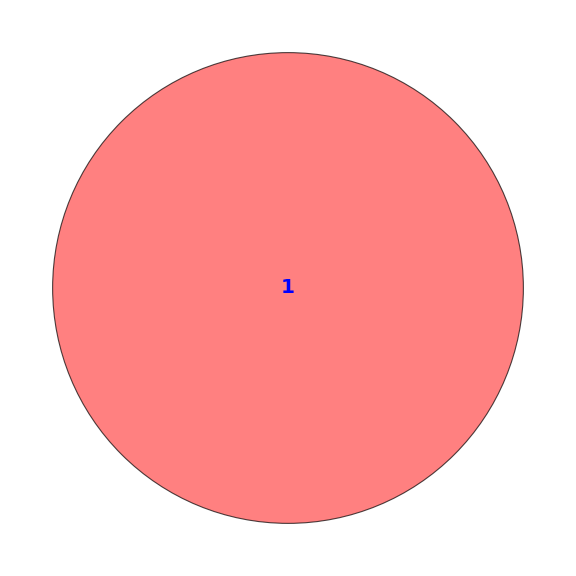
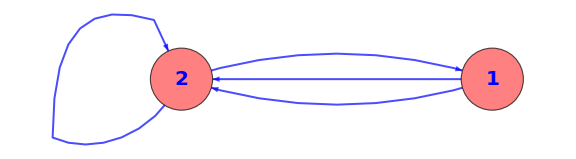
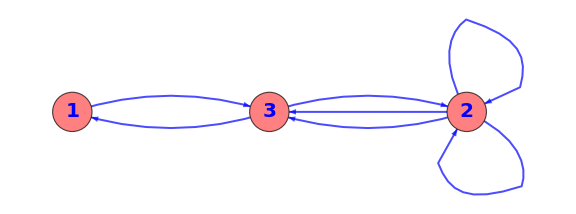
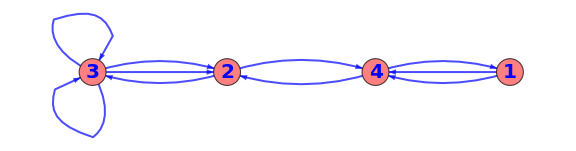
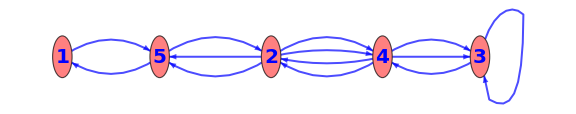
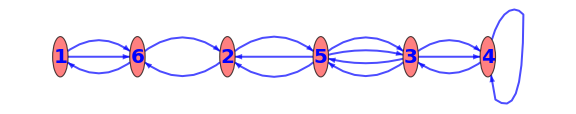
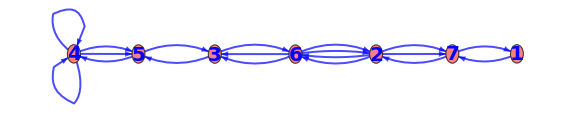
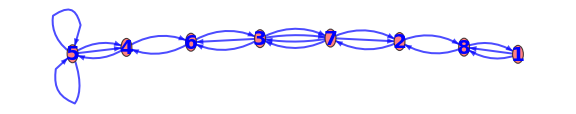

```mathematica
(*The matrices and weighted graphs for G*)
k:=10;
Table[G[i]//MatrixForm,{i,1,k}]
Table[GraphForG[i]//MatrixForm,{i,1,k}]
```

{(0 | 1
a | 0),(0 | 0 | 1 | 0
0 | 0 | 0 | 1
a | 1 | 0 | 0
0 | a | 0 | 0),(0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 1
a | 1 | 0 | 0 | 0 | 0
0 | a | 1 | 0 | 0 | 0
0 | 0 | a | 0 | 0 | 0),(0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
a | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | a | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | a | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | a | 0 | 0 | 0 | 0),(0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
a | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | a | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | a | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | a | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | a | 0 | 0 | 0 | 0 | 0),(0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
a | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | a | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | a | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | a | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | a | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | a | 0 | 0 | 0 | 0 | 0 | 0),(0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
a | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | a | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | a | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | a | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | a | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | a | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | a | 0 | 0 | 0 | 0 | 0 | 0 | 0),(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
a | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | a | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | a | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | a | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | a | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | a | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | a | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | a | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0),(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
a | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | a | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | a | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | a | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | a | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | a | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | a | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | a | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | a | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0),(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
a | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | a | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | a | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | a | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | a | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | a | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | a | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | a | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | a | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | a | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)}

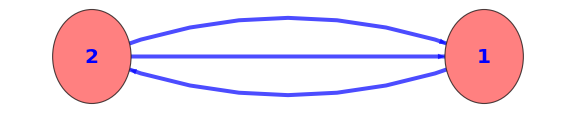
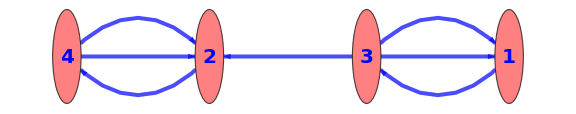
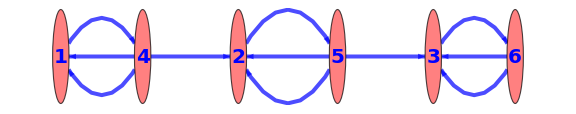
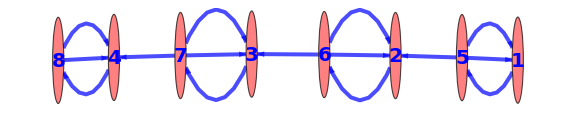
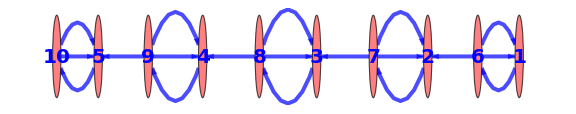
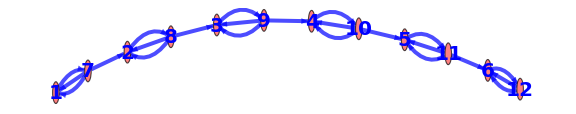
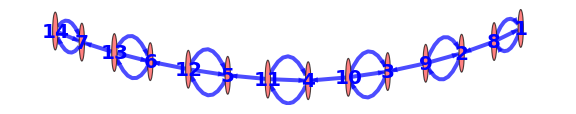
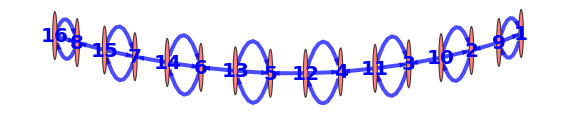

```mathematica
(*The matrices and weighted graphs for H*)
k:=10;
Table[H[a,i]//MatrixForm,{i,1,k}]
Table[GraphForH[2,i]//MatrixForm,{i,1,k}]
```

```mathematica
(*The value of the trace condition for the first few G*)
k:=10;
Table[ToSolve[G[i]],{i,1,k}]
```

{1,-2,3,-4,5,-6,7,-8,9,-10}

```mathematica
(*The value of the trace condition for the first few H*)
k:=10;
Table[ToSolve[H[a,i]],{i,1,k}]
```

{1/a+a,2/a+2 a,3/a+3 a,4/a+4 a,5/a+5 a,6/a+6 a,7/a+7 a,8/a+8 a,9/a+9 a,10/a+10 a}

```mathematica
(*The behavior under direct sums*)
ToSolve[DiSum[H[a,3],H[b,4]]]
ToSolve[DiSum[H[a,3],H[b,5]]]
ToSolve[DiSum[G[3],H[b,3]]]
ToSolve[DiSum[G[4],H[b,3]]]
```

3/a+3 a+4/b+4 b

3/a+3 a+5/b+5 b

3+3/b+3 b

-4+3/b+3 b

```mathematica
(*Solution of the trace condition for n=2*)
Solve[ToSolve[G[2]]==-q-q^(-1),q]
Solve[ToSolve[DiSum[G[1],G[1]]]==-q-q^(-1),q]
Solve[ToSolve[H[a,1]]==-q-q^(-1),q]
```

{{q→1},{q→1}}

{{q→-1},{q→-1}}

{{q→-1/a},{q→-a}}

```mathematica
(*Solution of the trace condition for n=3*)
Solve[ToSolve[G[3]]==-q-q^(-1),q]
Solve[ToSolve[DiSum[G[2],G[1]]]==-q-q^(-1),q]
Solve[ToSolve[DiSum[DiSum[G[1],G[1]],G[1]]]==-q-q^(-1),q]
Solve[ToSolve[DiSum[H[a,1],G[1]]]==-q-q^(-1),q]
```

{{q→1/2 (-3-√5)},{q→1/2 (-3+√5)}}

{{q→(-1)^(1/3)},{q→-(-1)^(2/3)}}

{{q→1/2 (-3-√5)},{q→1/2 (-3+√5)}}

{{q→(-1-a-a^2-√(1+2 a-a^2+2 a^3+a^4))/(2 a)},{q→(-1-a-a^2+√(1+2 a-a^2+2 a^3+a^4))/(2 a)}}

```mathematica
(*Infinitely many solutions of the trace condition for n=4 and q=1*)
Solve[ToSolve[DiSum[H[a,1],H[1,1]]]==-2,a]
Solve[ToSolve[DiSum[H[a,1],H[2,1]]]==-2,a]
Solve[ToSolve[DiSum[H[a,1],H[3,1]]]==-2,a]
Solve[ToSolve[DiSum[H[a,1],H[4,1]]]==-2,a]
```

{{a→-2-√3},{a→-2+√3}}

{{a→1/4 (-9-√65)},{a→1/4 (-9+√65)}}

{{a→1/3 (-8-√55)},{a→1/3 (-8+√55)}}

{{a→1/8 (-25-√561)},{a→1/8 (-25+√561)}}